```mathematica
sol=NDSolve[{m l[t] α'[t]^2==M(g+l''[t])Exp[-μ(π/2+α[t])]-m g Sin[α[t]],l'[t]α'[t]+l[t]α''[t]==g Cos[α[t]],α[0]==α'[0]==l'[0]==0,l[0]==0.8}/.m->0.02/.M->0.4/.g->9.8/.μ->0.24,{l,α},{t,0,5},WorkingPrecision->20,PrecisionGoal->20]
```

NDSolve::precw: The precision of the differential equation ({0.02` l[t] SuperscriptBox[{}{}{}{}) is less than WorkingPrecision (20.).

{{l→InterpolatingFunction[{{0, 5.0000000000000000000}}, <>],α→InterpolatingFunction[{{0, 5.0000000000000000000}}, <>]}}

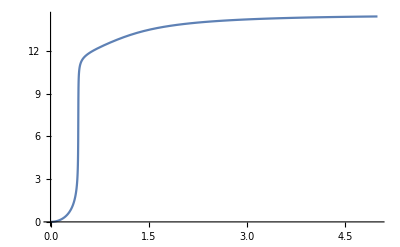

```mathematica
Plot[{α[t]}/.sol,{t,0,5},PlotRange->All]
```

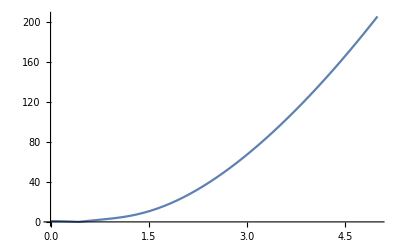

```mathematica
Plot[l[t]/.sol,{t,0,5}]
```